```mathematica
Coildir="Quad_Dump";
CoilTag="QUAD"
expfact=100;
```

QUAD

```mathematica
fn=FileNames[FileNameJoin[{NotebookDirectory[],Coildir,"*.dat"}]][[1]];
```

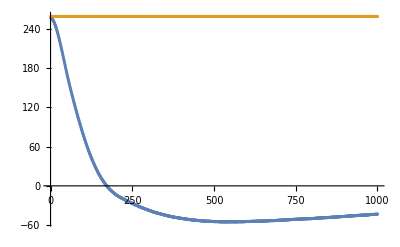

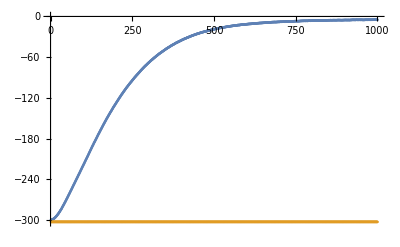

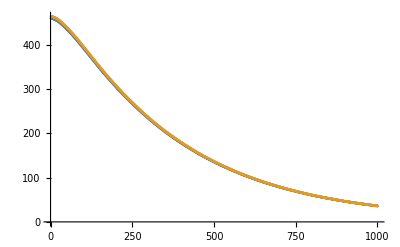

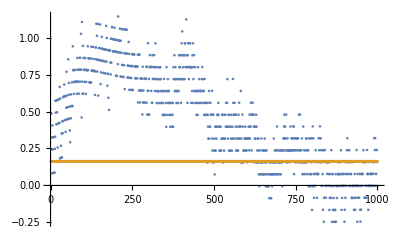

```mathematica
Module[{coils,tmp,coeffs,idx,idx2,offset,currs,outfn,exptbl,tmpinterp},
coils={"BUCK","PINCH","QUAD","OCT"};
ass=AssociationThread[coils->Table[{},{Length[coils]}]];
tmp=Import[fn];
coeffs=tmp[[2]][[11;;]];
offset=tmp[[Length[tmp]-2]];
For[idx=6,idx≤(Length[tmp]-2),idx++,If[Reverse[tmp[[idx]]][[3]]<0,Break[];];];
While[idx≤(Length[tmp]-2),
currs=(tmp[[idx]][[{32,31,33,34,35}]]-offset[[{32,31,33,34,35}]])*tmp[[2]][[11;;]];
currs[[4]]+=currs[[5]];
For[idx2=1,idx2≤Length[coils],idx2++,
AppendTo[ass[coils[[idx2]]],currs[[idx2]]];
];
idx++;
];
ass["PINCH"]*=-1;

Do[
outfn=FileNameJoin[{NotebookDirectory[],Coildir,"Dump_"<>coilnm<>".bin"}];
tmpinterp=Interpolation[ass[coilnm]];
exptbl=Table[tmpinterp[If[coilnm==CoilTag,x/expfact ,1]],{x,expfact,expfact*Length[ass[coilnm]]}];
BinaryWrite[outfn,exptbl,"Real64"];
Close[outfn];
lim=1000;
Print[ListPlot[{ass[coilnm][[1;;lim]],1.01*exptbl[[1;;expfact*lim;;expfact]]},PlotRange->Full]];
,{coilnm,coils}];
];
```